```mathematica
Using multiple torrus could be a new cryptography algorithm.  The 3d coordinates could be given for points on torroidal surfaces, and then within certail areas of the torrus would be certail letters of the alphabet.  Different modifications could allow for multiple transcriptions.  The surface could be letter parameterized differently every hour or day.  Not all letters might be parameterized on a single surface or face of a surface.  Therefore a translated torrus would then be utilized.  The directionality with respect to the original torus, could dictate the parameterization of that specific torrus' surface.  The number of torrus per period in each cryptographic space would then be dictated and depend on the thickness of a single torrus in 3D space.
```

```mathematica
R=5;
r=2;
```

```mathematica
x[u_,v_,R_,r_]=(R+r*Cos[v])*Cos[u]
```

Cos[u] (R+r Cos[v])

```mathematica
y[u_,v_,R_,r_]=(R+r*Cos[v])*Sin[u]
```

(R+r Cos[v]) Sin[u]

```mathematica
z[u_,v_,r_]=r*Sin[v]
```

r Sin[v]

```mathematica
Manipulate[ParametricPlot3D[{x[u,v,R,r],y[u,v,R,r],z[u,v,r]},{u,0,2*Pi},{v,0,2*Pi},PlotRange->12],{r,1,4},{R,5,8}]
```

```mathematica
Perhaps the function should be a periodic extension of these two functions.
```

```mathematica
r0[t_]=Sinh[t]/(1+Cosh[t]);
```

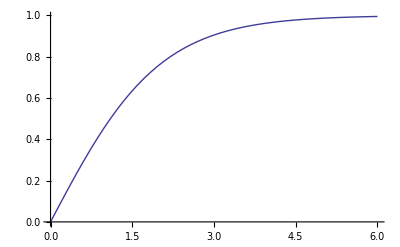

```mathematica
Plot[Sinh[t]/(1+Cosh[t]),{t,0,6}]
```

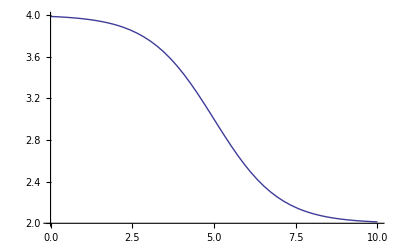

```mathematica
Plot[2+1-Tanh[(t-5)/2],{t,0,10}]
```

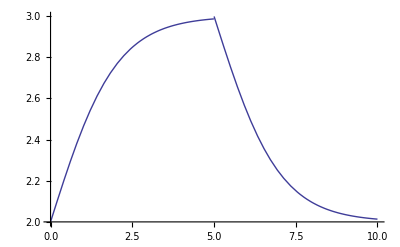

```mathematica
Plot[Piecewise[{{2+Sinh[t]/(1+Cosh[t]),t<5},{2+1-Tanh[(t-5)/2],t>5}}],{t,0,10}]
```

```mathematica
Is this some sort of modified sawtooth wave?
```

```mathematica
r[t_]=Piecewise[{{2+Sinh[t]/(1+Cosh[t]),t<5},{2+1-Tanh[(t-5)/2],t==5}},2+1-Tanh[(t-5)/2]];
```

```mathematica
x[u_,v_,R_,t_]=(R+r[t]*Cos[v])*Cos[u];
```

```mathematica
y[u_,v_,R_,t_]=(R+r[t]*Cos[v])*Sin[u];
```

```mathematica
z[u_,v_,t_]=r[t]*Sin[v];
```

```mathematica
Manipulate[ParametricPlot3D[{x[u,v,R,t],y[u,v,R,t],z[u,v,t]},{u,0,2*Pi},{v,0,2*Pi},PlotRange->20],{t,0,10},{R,15,20}]
```

```mathematica
I could parameterize the rotation by changing weather the Sin or Cos of u is used in x or y and how much phase of each is used.  Possibly do this parameterization through the nth power of -1 and the nth derivative.  ...Thoughts on scaling?
```